### Potassium Potentials

#### Singlet

Energies in cm^-1 and lengths in Å

```mathematica
Rin = 2.870;
Asg = -0.263145571*10^4;
Bsg = 0.813723194*10^9;
Ns = 12;
Rout = 12.000;
b = -0.40;
Rm = 3.92436437;
acf = {−4450.899484,0.30601009538111*10^-1,0.13671217000518*10^5,0.10750910095361*10^5,−0.20933401680991*10^4,−0.19385874804675*10^5,−0.49208915890513*10^5,0.11026639220148*10^6,0.72867339500920*10^6,−0.29310679369135*10^7,−0.12407070106619*10^8,0.40333947198094*10^8,0.13229848871390*10^9,−0.37617673798775*10^9,−0.95250413275787*10^9, 0.24655585744641*10^(10),0.47848257695164*10^(10),−0.11582132109947*10^(11),−0.17022518297651*10^(11),0.39469335034593*10^(11),0.43141949844339*10^(11),−0.97616955325128*10^(11),−0.77417530685917*10^(11),0.17314133615879*10^(12), 0.96118849114926*10^(11),−0.21425463041449*10^(12),−0.78513081754125*10^(11),0.17539493131251*10^(12),0.37939637008662*10^(11),−0.85271868691526*10^(11),−0.82123523240949*10^(10),0.18626451751424*10^(11)};
C6 = 0.1892652670*10^8;
C8 = 0.5706799527*10^9;
C10=0.1853042722*10^11;
Aex = 0.90092159*10^4;
gamma = 5.19500;
beta = 2.13539;
nucf = {0.13148609,2.08523853};
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
amu = 1822.89;
massK39 = 38.963708*amu;
massK40 =39.964008*amu;
mu39 = massK39/2;
mu40 = massK40/2;
```

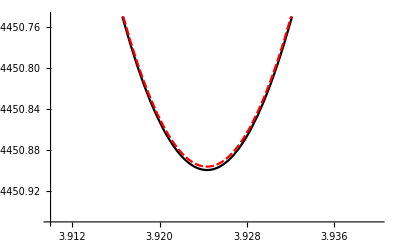

```mathematica
ξ[r_]:= (r-Rm)/(r+b Rm);
uIR[r_]:= Sum[acf[[i+1]]*(ξ[r])^i,{i,0,Length[acf]-1}];
uSR[r_]:= Asg+Bsg/r^Ns;
uLR[r_]:= -C6/r^6-C8/r^8-C10/r^10-Aex r^gamma Exp[-beta r];
Uad[r_]:= (1-mu39/mu40)*((2 Rm)/(r+Rm))^6*Sum[nucf[[i+1]]*(ξ[r])^i,{i,0,Length[nucf]-1}];
SingletK39[r_]:=Piecewise[{{uSR[r],0<r≤Rin},{uIR[r],Rin<r<Rout},{uLR[r],Rout≤ r}}];
SingletK40[r_]:= SingletK39[r]+Uad[r];
Plot[{SingletK39[r],SingletK40[r]},{r,3.91,3.94},PlotRange->{-4450.95,-4450.75},PlotStyle->{Black,Red}]
```

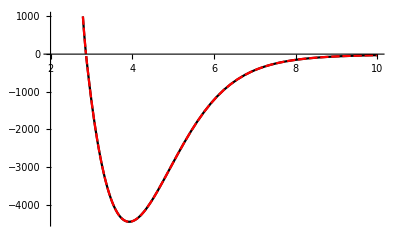

```mathematica
Plot[{SingletK39[r],SingletK40[r]},{r,2,10},PlotRange->{-4455,1000},PlotStyle->{Black,Red}]
```

##### Convert to atomic units

```mathematica
C6au = C6*invcminHartree*(AngstrominBohr)^6;
C8au = C8*invcminHartree*(AngstrominBohr)^8;
C10au = C10*invcminHartree*(AngstrominBohr)^10;
```

```mathematica
rmax=700;
rmin=0.005;
NR =10000;
dR=(rmax-rmin)/NR;
RGrid =Table[rmin+dR i,{i,1,NR}];
```

```mathematica
SingletK39Newdat = Table[{RGrid[[i]]*AngstrominBohr,SingletK39[RGrid[[i]]]*invcminHartree},{i,1,NR}];
SingletK40Newdat = Table[{RGrid[[i]]*AngstrominBohr,SingletK40[RGrid[[i]]]*invcminHartree},{i,1,NR}];
SingletK39New = Interpolation[SingletK39Newdat];
SingletK40New = Interpolation[SingletK40Newdat];
```

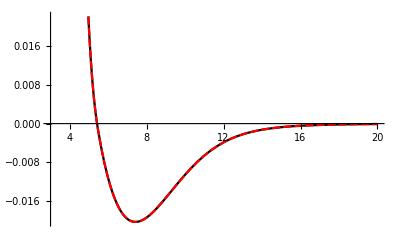

```mathematica
Plot[{SingletK39New[r],SingletK40New[r]},{r,3,20},PlotStyle->{Black,Red}]
```

##### Scattering Lengths

```mathematica
CalcCotanDelta[Εtest_,rmax_,rmin_,μ_,U_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2,u},
r1=0.95 rmax;
r2=0.99rmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[r]+U[r] u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]

CalcERE[rmax_,rmin_,ΕMin_,ΕMax_,μ_,U_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcCotanDelta[Εtest,rmax,rmin,μ,U]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
{Singlet39ascat,Singlet39reff,Singlet39EREData}=CalcERE[300,3,10^-12,10^-10,mu39,SingletK39New]
```

{137.358,78.7649,{{7.10266×10^-8,-0.00727722},{7.74189×10^-7,-0.00724966},{1.47735×10^-6,-0.00722207},{2.18052×10^-6,-0.00719445},{2.88368×10^-6,-0.0071668},{3.58684×10^-6,-0.00713913},{4.29×10^-6,-0.00711142},{4.99317×10^-6,-0.00708368},{5.69633×10^-6,-0.00705592},{6.39949×10^-6,-0.00702812},{7.10266×10^-6,-0.0070003}}}

```mathematica
{Singlet40ascat,Singlet40reff,Singlet40EREData}=CalcERE[300,3,10^-12,10^-10,mu40,SingletK40New]
```

{104.877,65.6562,{{7.285×10^-8,-0.00953244},{7.94065×10^-7,-0.00950886},{1.51528×10^-6,-0.00948525},{2.23649×10^-6,-0.00946162},{2.95771×10^-6,-0.00943798},{3.67892×10^-6,-0.00941431},{4.40014×10^-6,-0.00939063},{5.12135×10^-6,-0.00936692},{5.84257×10^-6,-0.00934319},{6.56378×10^-6,-0.00931945},{7.285×10^-6,-0.00929568}}}

#### Triplet

```mathematica
Rin3 = 4.750;
A3 =−0.6948000684*10^3;
B3 = 0.7986755824*10^7;
Ns3=6;
b3 = -0.300;
Rm3 = 5.73392370;
a3cf={−255.015289,−0.84057856111142,0.20960112217307*10^4,−0.17090298954603*10^4,−0.17873773359495*10^4,0.29451253739583*10^4,−0.20200089247397*10^5,−0.35699524005434*10^5,0.59869055371895*10^6,−0.71054353363636*10^6,−0.61711841390175*10^7,0.19365507566961*10^8,0.67930587059121*10^7,−0.12020061704172*10^9,0.21603959986951*10^9,−0.63531969223760*10^8,−0.52391212820709*10^9,0.15913304648629*10^(10),−0.24792546567713*10^(10),0.20326031881106*10^(10),−0.68044508325774*10^9};
nu3 = 0.23803737;
```

```mathematica
Length[a3cf]
```

21

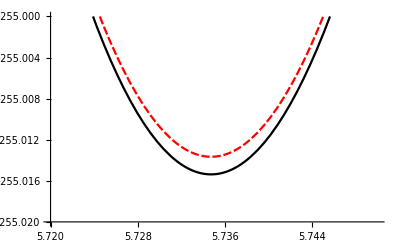

```mathematica
ξ3[r_]:= (r-Rm3)/(r+b3 Rm3);
uIR3[r_]:= Sum[a3cf[[i+1]]*(ξ3[r])^i,{i,0,Length[a3cf]-1}];
uSR3[r_]:= A3 +B3/r^Ns3;
uLR3[r_]:= -C6/r^6-C8/r^8-C10/r^10+Aex r^gamma Exp[-beta r];
Uad3[r_]:= (1-mu39/mu40)*((2 Rm)/(r+Rm))^6*nu3;
TripletK39[r_]:=Piecewise[{{uSR3[r],0<r≤Rin3},{uIR3[r],Rin3<r<Rout},{uLR3[r],Rout≤ r}}];
TripletK40[r_]:= TripletK39[r]+Uad3[r];
Plot[{TripletK39[r],TripletK40[r]},{r,5.72,5.75},PlotRange->{-255.02,-255},PlotStyle->{Black,Red}]
```

##### Atomic Units

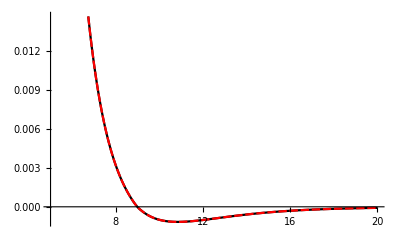

```mathematica
TripletK39Newdat = Table[{RGrid[[i]]*AngstrominBohr,TripletK39[RGrid[[i]]]*invcminHartree},{i,1,NR}];
TripletK40Newdat = Table[{RGrid[[i]]*AngstrominBohr,TripletK40[RGrid[[i]]]*invcminHartree},{i,1,NR}];
TripletK39New = Interpolation[TripletK39Newdat];
TripletK40New = Interpolation[TripletK40Newdat];
Plot[{TripletK39New[r],TripletK40New[r]},{r,5,20},PlotStyle->{Black,Red}]
```

##### Scattering Lengths

```mathematica
{Triplet39ascat,Triplet39reff,Triplet39EREData}=CalcERE[600,3,10^-12,10^-10,mu39,TripletK39New]
```

{-33.2795,1999.57,{{7.10266×10^-8,0.0302289},{7.74189×10^-7,0.0308681},{1.47735×10^-6,0.0315202},{2.18052×10^-6,0.0321859},{2.88368×10^-6,0.0328656},{3.58684×10^-6,0.0335597},{4.29×10^-6,0.0342688},{4.99317×10^-6,0.0349933},{5.69633×10^-6,0.0357338},{6.39949×10^-6,0.0364909},{7.10266×10^-6,0.0372651}}}

```mathematica
{Triplet40ascat,Triplet40reff,Triplet40EREData}=CalcERE[600,3,10^-12,10^-10,mu40,TripletK40New]
```

{169.262,91.6153,{{7.285×10^-8,-0.00590431},{7.94065×10^-7,-0.00587148},{1.51528×10^-6,-0.0058386},{2.23649×10^-6,-0.00580568},{2.95771×10^-6,-0.00577271},{3.67892×10^-6,-0.00573969},{4.40014×10^-6,-0.00570663},{5.12135×10^-6,-0.00567353},{5.84257×10^-6,-0.00564038},{6.56378×10^-6,-0.00560718},{7.285×10^-6,-0.00557394}}}

### K39 and K40 Data

```mathematica
K39s = 1/2;
K40s = K39s;
K39i = 3/2;
K40i = 4;
K40gs =  2.002319313470;
K39gs = K40gs;
K40gi = 0.00017649034;
K39gi = -0.00014193489;
```

```mathematica
K39AMHz =230.85986013;
K40AMHz =-285.730824;
```

```mathematica
μbMHz = (9.27*10^-24)/(6.626*10^-34)*10^-10;
```

```mathematica
K39ATHz = K39AMHz*10^-6;
K40ATHz = K40AMHz*10^-6;
K39Ainvcm = (K39ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
K40Ainvcm = (K40ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
K39AH = K39Ainvcm*invcminHartree;
K40AH = K40Ainvcm*invcminHartree;
μbTHz = μbMHz *10^-6;
μbinvcm = (μbTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μbH=μbinvcm*invcminHartree
```

2.12675×10^-10

#### Single Atom Hyperfine and Zeeman Structure

```mathematica
K39AH
```

3.50943×10^-8

```mathematica
K40AH
```

-4.34355×10^-8

```mathematica
K39HFbasis = Flatten[Table[Table[{f, mf},{mf,-f,f}],{f,1,2}],1]
```

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
K40HFbasis = Flatten[Table[Table[{f, mf},{mf,-f,f}],{f,7/2,9/2}],1]
```

{{7/2,-7/2},{7/2,-5/2},{7/2,-3/2},{7/2,-1/2},{7/2,1/2},{7/2,3/2},{7/2,5/2},{7/2,7/2},{9/2,-9/2},{9/2,-7/2},{9/2,-5/2},{9/2,-3/2},{9/2,-1/2},{9/2,1/2},{9/2,3/2},{9/2,5/2},{9/2,7/2},{9/2,9/2}}

```mathematica
K40HF2Atombasis =  Flatten[Table[Table[{f1, mf1,f2,mf2},{mf1,-f1,f1},{mf2,-f2,f2}],{f1,7/2,9/2},{f2,7/2,9/2}],3];
```

```mathematica
Select[K40HF2Atombasis,#[[2]]+#[[4]]==-8&]
```

{{7/2,-7/2,9/2,-9/2},{9/2,-9/2,7/2,-7/2},{9/2,-9/2,9/2,-7/2},{9/2,-7/2,9/2,-9/2}}

```mathematica
Hhf[A_,i_,s_,f_,ℏ_]:= A/2 ℏ^2(f(f+1)-s(s+1)-i(i+1));
Hz[fp_,mp_,f_,m_,gi_,gs_,s_,i_,B_]:= gs μbH B √((2 fp +1)(2f +1)) Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]-gi μbH B √((2 fp +1)(2f +1)) Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

##### Potassium 39

```mathematica
HhfK39Table=Table[Hhf[K39AH,K39i,K39s,K39HFbasis[[j,1]],1]KroneckerDelta[j,jp],{j,1,8},{jp,1,8}];
```

```mathematica
HzK39Table[B_]:= Table[Hz[K39HFbasis[[jp,1]],K39HFbasis[[jp,2]],K39HFbasis[[j,1]],K39HFbasis[[j,2]],K39gi,K39gs,K39s,K39i,B],{j,1,8},{jp,1,8}];
```

```mathematica
HK39[B_]:= HzK39Table[B] + HhfK39Table;
```

```mathematica
K39AtomEigenSystem[B_]:=Sort[Transpose[Eigensystem[HK39[B]]]]
K39AtomEth[B_]:=Table[K39AtomEigenSystem[B][[i]][[1]],{i,1,8}]
K39EigenSystem[B_]:=Sort[Eigenvalues[HK39[B]]];
```

```mathematica
K39EigenSystem[0.1]
```

{-4.38785×10^-8,-4.38679×10^-8,-4.38572×10^-8,2.62994×10^-8,2.63101×10^-8,2.63207×10^-8,2.63314×10^-8,2.6342×10^-8}

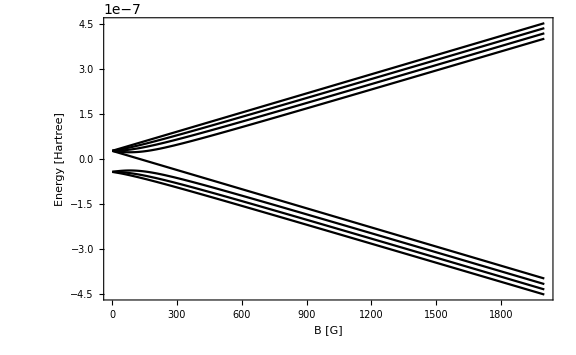

```mathematica
Plot[K39EigenSystem[B],{B,1,2000}, Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},ImageSize->Large,LabelStyle->Large ]
```

##### Potassium 40

```mathematica
HhfK40Table=Table[Hhf[K40AH,K40i,K40s,K40HFbasis[[j,1]],1]KroneckerDelta[j,jp],{j,1,Length[K40HFbasis]},{jp,1,Length[K40HFbasis]}];
HzK40Table[B_]:= Table[Hz[K40HFbasis[[jp,1]],K40HFbasis[[jp,2]],K40HFbasis[[j,1]],K40HFbasis[[j,2]],K40gi,K40gs,K40s,K40i,B],{j,1,Length[K40HFbasis]},{jp,1,Length[K40HFbasis]}];
```

```mathematica
HK40[B_]:= HzK40Table[B] + HhfK40Table;
K40AtomEigenSystem[B_]:=Sort[Transpose[Eigensystem[HK40[B]]]];
K40AtomEth[B_]:=Table[K40AtomEigenSystem[B][[i]][[1]],{i,1,Length[K40HFbasis]}];
K40EigenSystem[B_]:=Sort[Eigenvalues[HK40[B]]];
```

```mathematica
Length[K40HFbasis]
```

18

```mathematica
Plot[K40EigenSystem[B],{B,0,800}, Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},ImageSize->Large,LabelStyle->Large]
```

$Aborted

#### K-39 Collision

Basis and projection operators

```mathematica
K39MF2basis = {{1,1,1,1},{1,1,2,1},{1,0,2,2},{2,0,2,2},{2,1,2,1}};
K39SingletProjection={{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,-3/16},{(√(3/2))/8,1/8,-1/(4 √2),1/(4 √2),-(√(3/2))/8},{-(√3)/8,-1/(4 √2),1/4,-1/4,(√3)/8},{(√3)/8,1/(4 √2),-1/4,1/4,-(√3)/8},{-3/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16}};
K39TripletProjection={{13/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16},{-(√(3/2))/8,7/8,1/(4 √2),-1/(4 √2),(√(3/2))/8},{(√3)/8,1/(4 √2),3/4,1/4,-(√3)/8},{-(√3)/8,-1/(4 √2),1/4,3/4,(√3)/8},{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,13/16}};
```

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_,μb_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μb B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]-gi μb B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[K39MF2basis[[j,1]],K39MF2basis[[j,3]]] KroneckerDelta[K39MF2basis[[j,2]],K39MF2basis[[j,4]]])(1+KroneckerDelta[K39MF2basis[[jp,1]],K39MF2basis[[jp,3]]] KroneckerDelta[K39MF2basis[[jp,2]],K39MF2basis[[jp,4]]]))))*(HZ[K39MF2basis[[j,1]],K39MF2basis[[j,2]],K39MF2basis[[jp,1]],K39MF2basis[[jp,2]],K39s,K39i,K39gs,K39gi,K39AH,B,μbH]KroneckerDelta[K39MF2basis[[j,3]],K39MF2basis[[jp,3]]]KroneckerDelta[K39MF2basis[[j,4]],K39MF2basis[[jp,4]]]+HZ[K39MF2basis[[j,3]],K39MF2basis[[j,4]],K39MF2basis[[jp,3]],K39MF2basis[[jp,4]],K39s,K39i,K39gs,K39gi,K39AH,B,μbH]KroneckerDelta[K39MF2basis[[j,1]],K39MF2basis[[jp,1]]]KroneckerDelta[K39MF2basis[[j,2]],K39MF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[K39MF2basis[[j,3]],K39MF2basis[[j,4]],K39MF2basis[[jp,1]],K39MF2basis[[jp,2]],K39s,K39i,K39gs,K39gi,K39AH,B,μbH]KroneckerDelta[K39MF2basis[[j,1]],K39MF2basis[[jp,3]]]KroneckerDelta[K39MF2basis[[j,2]],K39MF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[K39MF2basis[[j,1]],K39MF2basis[[j,2]],K39MF2basis[[jp,3]],K39MF2basis[[jp,4]],K39s,K39i,K39gs,K39gi,K39AH,B,μbH]KroneckerDelta[K39MF2basis[[j,3]],K39MF2basis[[jp,1]]]KroneckerDelta[K39MF2basis[[j,4]],K39MF2basis[[jp,2]]]),{j,1,Length[K39MF2basis]},{jp,1,Length[K39MF2basis]}]
```

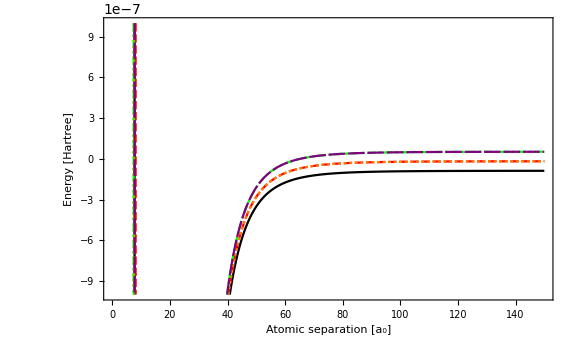

```mathematica
HZK39[B_]=FullSimplify[HZsym[0,0,B]];
Htotal[r_,B_]= HZK39[B]+K39TripletProjection*TripletK39New[r]+K39SingletProjection*SingletK39New[r];
Plot[{ Htotal[r, 0][[1, 1]], Htotal[r, 0][[2, 2]],Htotal[r, 0][[3, 3]],Htotal[r, 0][[4, 4]],Htotal[r, 0][[5, 5]]},{r,5,150},Frame->True,ImageSize->Large,FrameLabel->{"Atomic separation [a_0]","Energy [Hartree]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple},PlotRange->{-1*10^-6,1*10^-6}]
```

```mathematica
βK39
```

βK39

```mathematica
Plot[{ Htotal[r βK39, 0][[1, 1]]HartreeinK39vdw, Htotal[r βK39, 0][[2, 2]]HartreeinK39vdw,Htotal[r βK39, 0][[3, 3]]HartreeinK39vdw,Htotal[r βK39, 0][[4, 4]]HartreeinK39vdw,Htotal[r βK39, 0][[5, 5]]HartreeinK39vdw},{r,.05,1.0},Frame->True,ImageSize->Large,FrameLabel->{"Atomic separation [β_vdW]","Energy [E_vdW]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple},PlotRange->{-5000,5000}]
```

-Graphics-

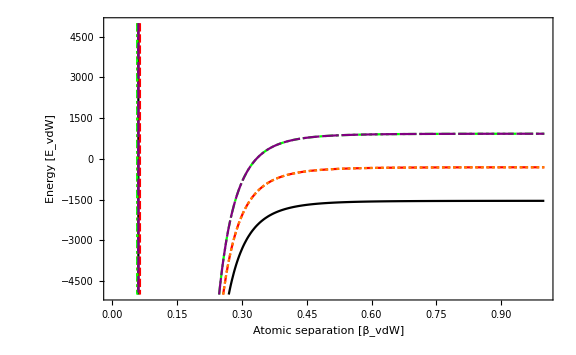

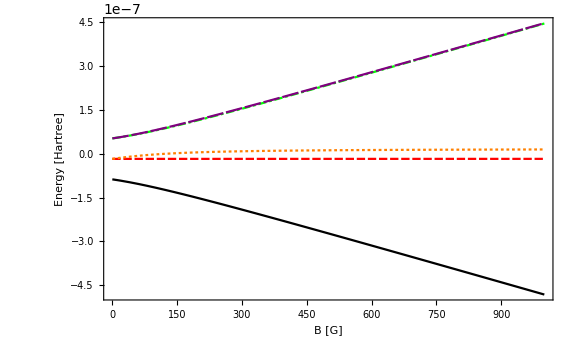

```mathematica
EigenSystemK39[B_]:= Sort[Transpose[Eigensystem[HZK39[B]]]];
Plot[{EigenSystemK39[B][[1]][[1]],EigenSystemK39[B][[2]][[1]],EigenSystemK39[B][[3]][[1]],EigenSystemK39[B][[4]][[1]],EigenSystemK39[B][[5]][[1]]},{B,0,1000},ImageSize->Large,Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple}]
```

##### van der Waals units

```mathematica
βK39 = β/.Solve[-C6au/β^6-C8au/β^8-C10au/β^10==-1/(2 mu39 β^2),β][[8]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

129.442

```mathematica
BohrinK39vdw = 1/129.44206700947666
K39vdwinHartree = 1/(2 mu39 βK39^2);
HartreeinK39vdw = 1/K39vdwinHartree
```

0.00772546

1.19007×10^9

```mathematica
C6vdw = (2 mu39)/βK39^4(C6au)
C8vdw = (2 mu39)/βK39^6(C8au)
C10vdw = (2 mu39)/βK39^8(C10au)
```

0.993571

0.00638509

0.0000441883

```mathematica
μbvdw = μbH*HartreeinK39vdw;
```

```mathematica
Triplet39VDWdat= Table[{TripletK39Newdat[[i,1]]*BohrinK39vdw, TripletK39Newdat[[i,2]]*HartreeinK39vdw},{i,1,Length[TripletK39Newdat]}];
Triplet39VDW= Interpolation[Triplet39VDWdat];
Singlet39VDWdat= Table[{SingletK39Newdat[[i,1]]*BohrinK39vdw, SingletK39Newdat[[i,2]]*HartreeinK39vdw},{i,1,Length[SingletK39Newdat]}];
Singlet39VDW= Interpolation[Singlet39VDWdat];
```

```mathematica
K39vlr[r_]:= -C6vdw/r^6-C8vdw/r^8-C10vdw/r^10
```

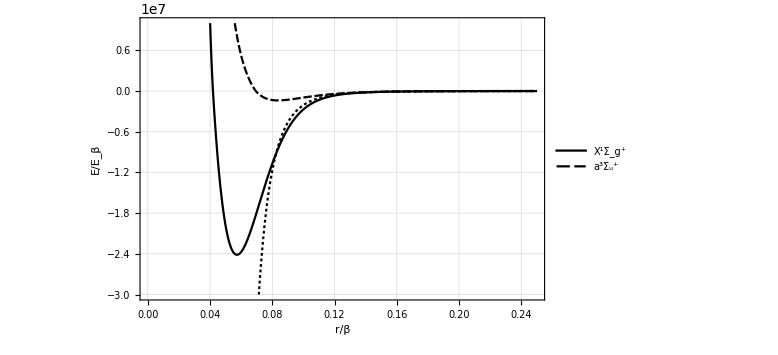

```mathematica
Plot[{Singlet39VDW[r],Triplet39VDW[r],K39vlr[r]},{r,0.02,0.25},PlotRange->{-3.0*10^7,10^7},ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"r/β","E/E_β"},LabelStyle->Medium,PlotLegends->{"X^1Σ_g^+","a^3Σ_u^+"}]
```

```mathematica
2 βK39
```

258.884

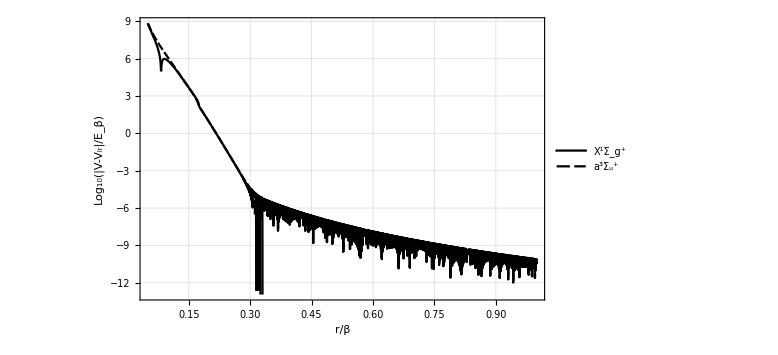

```mathematica
Plot[{Log[10,Abs[Singlet39VDW[r]-K39vlr[r]]],Log[10,Abs[Triplet39VDW[r]-K39vlr[r]]]},{r,0.05,1},(*PlotRange->{-3.0*10^7,10^7},*)ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"r/β","Log_10(|V-V_lr|/E_β)"},LabelStyle->Medium,PlotLegends->{"X^1Σ_g^+","a^3Σ_u^+"}]
```

```mathematica
χminus[r_,l_]:= Sqrt[r] BesselJ[1/4(2l+1),1/(2 r^2) ];
χmprime[r_,l_]:= D[χminus[rp,l],rp]/.rp->r;
f[l_,k_,r_]:=r SphericalBesselJ[l,k r];
g[l_,k_,r_]:= r SphericalBesselY[l,k r];
dfdr[l_,k_,r_]:=D[f[l,k,rp],rp]/.rp->r; 
dgdr[l_,k_,r_]:=D[g[l,k,rp],rp]/. rp->r; 
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=α';
g0=- α[r]Cos[ϕ+phaseint[r]];
f0= α[r]Sin[ϕ+phaseint[r]];
f0p=αp[r]/α[r] f0-1/α[r]^2 g0;
g0p=αp[r]/α[r] g0+1/α[r]^2 f0;
χm=χminus[r,l];
χmp=χmprime[r,l];
{f0,g0,f0p,g0p,χm,χmp}]
```

```mathematica
60*BohrinK39vdw
```

0.463528

```mathematica
200*BohrinK39vdw
```

1.54509

```mathematica
rx = 0.05;
rf =1.7; (*200*BohrinK39vdw;*)
r0 =0.25;(* 60*BohrinK39vdw;*)
rmin = 2.0*BohrinK39vdw;
rmax = r0;
ltest = 0;
Etest = 10^-16; 
ksqr[Ε_,l_,r_]:=(Ε - K39vlr[r]-(l(l+1))/r^2);
BC1[Ε_,l_,r_,rx_]:=1/Sqrt[(Ε - K39vlr[r]-(l(l+1))/r^2)^(1/2)]/.r->rx;
BC2[Ε_,l_,r_,rx_]:=D[1/Sqrt[(Ε - K39vlr[r]-(l(l+1))/r^2)^(1/2)],r]/.r->rx;
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqr[Etest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[Etest,ltest,r,rx],α'[rx]==BC2[Etest,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,2}]];
α0fun=Table[α/.α0sol[[i]],{i,1,Length[α0sol]}];
nr=300;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,2}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,2}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,2}],{rf,rGrid}]];
ϕK39=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}];
```

```mathematica
ϕK39[[1]]
```

0.829105

```mathematica
CalcQuantumDefect[Ε_,l_,rmin_,rmax_,r0_,rx_,rf_,r_,nr_,U_,ϕ_]:= Module[{phaseint,αp,rp,αfun,α,f0,f0p,g0,g0p,u,up,Y,Ksr,mu},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,r0}];
αp=αfun';
f0=α[r0]Sin[ϕ+phaseint];
g0=-α[r0]Cos[ϕ+phaseint];
g0p=αp[r0]/αfun[r0] g0+1/αfun[r0]^2 f0;
f0p=αp[r0]/αfun[r0] f0-1/αfun[r0]^2 g0;
u=NDSolveValue[{-u''[r]+ (U[r]+(l(l+1))/r^2)u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
up=u';
Y = up[r]/u[r]/.r->r0;
Ksr = (Y f0 -f0p)/(Y g0 -g0p);
mu = 1/π ArcTan[Ksr];
Return[mu]
]
```

```mathematica
K39SingletQD=CalcQuantumDefect[Etest,0,rmin,rmax,r0,rx,rf,r,nr,Singlet39VDW,ϕK39[[1]]]
K39TripletQD=CalcQuantumDefect[Etest,0,rmin,rmax,r0,rx,rf,r,nr,Triplet39VDW,ϕK39[[1]]]
```

-0.27858

0.317611

-0.281127,0.316194

```mathematica
K39Avdw=K39AH*HartreeinK39vdw;
K39HZVDW[p_,l_,B_]:=
Table[(1/(√((1+KroneckerDelta[K39MF2basis[[j,1]],K39MF2basis[[j,3]]] KroneckerDelta[K39MF2basis[[j,2]],K39MF2basis[[j,4]]])(1+KroneckerDelta[K39MF2basis[[jp,1]],K39MF2basis[[jp,3]]] KroneckerDelta[K39MF2basis[[jp,2]],K39MF2basis[[jp,4]]]))))*(HZ[K39MF2basis[[j,1]],K39MF2basis[[j,2]],K39MF2basis[[jp,1]],K39MF2basis[[jp,2]],K39s,K39i,K39gs,K39gi,K39Avdw,B,μbvdw]KroneckerDelta[K39MF2basis[[j,3]],K39MF2basis[[jp,3]]]KroneckerDelta[K39MF2basis[[j,4]],K39MF2basis[[jp,4]]]+HZ[K39MF2basis[[j,3]],K39MF2basis[[j,4]],K39MF2basis[[jp,3]],K39MF2basis[[jp,4]],K39s,K39i,K39gs,K39gi,K39Avdw,B,μbvdw]KroneckerDelta[K39MF2basis[[j,1]],K39MF2basis[[jp,1]]]KroneckerDelta[K39MF2basis[[j,2]],K39MF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[K39MF2basis[[j,3]],K39MF2basis[[j,4]],K39MF2basis[[jp,1]],K39MF2basis[[jp,2]],K39s,K39i,K39gs,K39gi,K39Avdw,B,μbvdw]KroneckerDelta[K39MF2basis[[j,1]],K39MF2basis[[jp,3]]]KroneckerDelta[K39MF2basis[[j,2]],K39MF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[K39MF2basis[[j,1]],K39MF2basis[[j,2]],K39MF2basis[[jp,3]],K39MF2basis[[jp,4]],K39s,K39i,K39gs,K39gi,K39Avdw,B,μbvdw]KroneckerDelta[K39MF2basis[[j,3]],K39MF2basis[[jp,1]]]KroneckerDelta[K39MF2basis[[j,4]],K39MF2basis[[jp,2]]]),{j,1,Length[K39MF2basis]},{jp,1,Length[K39MF2basis]}];
```

{-674.67,-20.7961,18.1135,631.919,633.077}

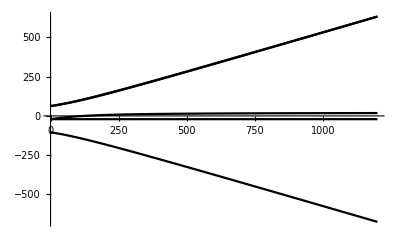

```mathematica
K39HZ[B_]=FullSimplify[K39HZVDW[0,0,B]];
K39HVDW[r_,B_]=K39HZ[B]+K39TripletProjection*Triplet39VDW[r]+K39SingletProjection*Singlet39VDW[r];
K39Eigensystem[B_]:= Sort[Transpose[Eigensystem[K39HZ[B]]]];
DD[B_]:= Transpose[{K39Eigensystem[B][[1]][[2]],K39Eigensystem[B][[2]][[2]],K39Eigensystem[B][[3]][[2]],K39Eigensystem[B][[4]][[2]],K39Eigensystem[B][[5]][[2]]}];
K39Eth[B_]:= Table[K39Eigensystem[B][[j]][[1]],{j,1,5}];
K39Eth[1200]
Plot[K39Eth[B],{B,0,1200}]
```

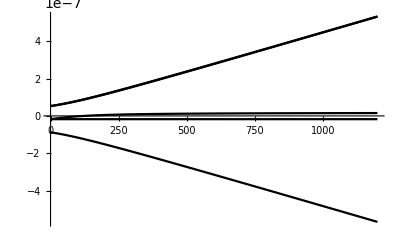

```mathematica
Plot[K39Eth[B]*1/HartreeinK39vdw,{B,0,1200}]
```

```mathematica
KsrFTEI[B_]:= Transpose[DD[B]].K39SingletProjection.DD[B]*Tan[π K39SingletQD 0.98] + Transpose[DD[B]].K39TripletProjection.DD[B]*Tan[π K39TripletQD 0.98]
```

```mathematica
MatrixForm[KsrFTEI[0]]
```

(0.989012 | 0.571614 | -0.404192 | 0.495032 | -0.571614
0.571614 | 0.824001 | 0.46672 | -0.571614 | 0.660042
-0.404192 | 0.46672 | 1.15402 | 0.404192 | -0.46672
0.495032 | -0.571614 | 0.404192 | 0.989012 | 0.571614
-0.571614 | 0.660042 | -0.46672 | 0.571614 | 0.824001)

```mathematica
KsrFTEIPP[B_]:=KsrFTEI[B][[1,1]];
KsrFTEIQP[B_]:=KsrFTEI[B][[2;;5,1]];
KsrFTEIPQ[B_]:=KsrFTEI[B][[1,2;;5]];
KsrFTEIQQ[B_]:=KsrFTEI[B][[2;;5,2;;5]];
```

```mathematica
En=200;
Emin = 10^-16;
Emax =1500;
EGrid=Table[Emin+((i-1)/(En-1))^3(Emax-Emin),{i,1,En}];
```

```mathematica
calcTanGamma[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{αfun,phaseint,g0,g0p,f0,f0p,αp,α,κ,rp,gbound,gboundp,tanγ},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
κ=√-Ε;
gbound=√(κ/π rp) BesselK[l+1/2,κ rp]/.rp->rf;
gboundp=D[√(κ/π rp) BesselK[l+1/2,κ rp],rp]/.rp->rf;
tanγ =-(gbound g0p-gboundp g0)/(gbound f0p - gboundp f0);
Return[tanγ]
]
```

```mathematica
gammaTable=Table[{-EGrid[[ii]],ArcTan[calcTanGamma[0,rx,rf,r,-EGrid[[ii]],ϕK39[[1]]]]},{ii,1,Length[EGrid]}];
```

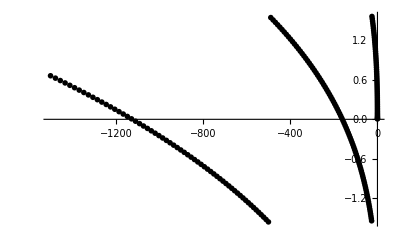

```mathematica
ListPlot[gammaTable,PlotRange->Full]
```

```mathematica
GammaTablenew=gammaTable;
For[i=1,i<Length[gammaTable],i++,
If[(gammaTable[[i+1,2]]-gammaTable[[i,2]]<-1.2),Print[i];
GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]+π,GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]]
]
```

52

138

```mathematica
Gammafun = Interpolation[GammaTablenew(*,InterpolationOrder->1*)];
```

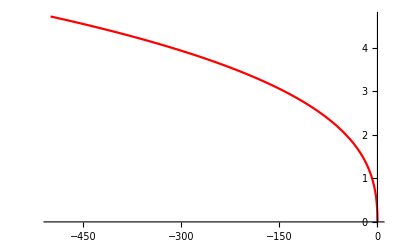

```mathematica
Plot[{Gammafun[ϵ]},{ϵ,-500,0},PlotStyle->{Black,Red}]
```

```mathematica
CotGamma2[B_,Ε_]:= Cot[Gammafun[((K39Eth[B][[1]]+Ε)-K39Eth[B][[2]])]];
CotGamma3[B_,Ε_]:= Cot[Gammafun[((K39Eth[B][[1]]+Ε)-K39Eth[B][[3]])]];
CotGamma4[B_,Ε_]:= Cot[Gammafun[((K39Eth[B][[1]]+Ε)-K39Eth[B][[4]])]];
CotGamma5[B_,Ε_]:= Cot[Gammafun[((K39Eth[B][[1]]+Ε)-K39Eth[B][[5]])]];
CotGammaMatrix[B_,Ε_]:=DiagonalMatrix[{CotGamma2[B,Ε],CotGamma3[B,Ε],CotGamma4[B,Ε],CotGamma5[B,Ε]}];
```

```mathematica
bmax = 1000;
bmin = 0;
bn = 500;
bgrid = Table[(bmax-bmin)/bn i,{i,0,bn}];
Etest = 10^-3;
KtildeFTEI[B_,Ε_]:= KsrFTEIPP[B]-KsrFTEIPQ[B].Inverse[KsrFTEIQQ[B]+CotGammaMatrix[B,Ε]].KsrFTEIQP[B];
```

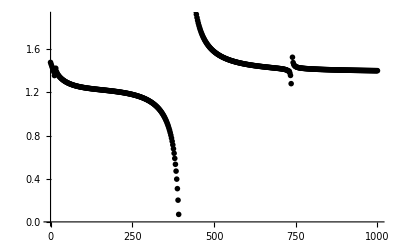

```mathematica
ListPlot[{Table[{bgrid[[ii]],KtildeFTEI[bgrid[[ii]],Etest]},{ii,1,bn+1}]}]
```

```mathematica
CalcTanEta[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,gs,fs,fsp,gsp,k,tanη,αfun,phaseint,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs =g[l,k,r];
gsp=dgdr[l,k,r];
tanη=(fs f0p-f0 fsp)/(gs f0p-f0 gsp)/.r->rf;
Return[tanη]
]
```

```mathematica
En2=100;
Emin2 = 10^-16;
Emax2=100;
EGrid2=Table[Emin2+((i-1)/(En2-1))^3(Emax2-Emin2),{i,1,En2}];
```

```mathematica
EtaTable=Table[{EGrid2[[ii]],ArcTan[CalcTanEta[ltest,rx,rf,r,EGrid2[[ii]],ϕK39[[1]]]]},{ii,1,Length[EGrid2]}];
```

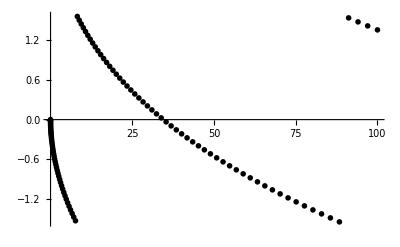

```mathematica
ListPlot[EtaTable]
```

```mathematica
EtaTablenew2=EtaTable;
For[i=1,i<Length[EtaTable],i++,
If[(EtaTable[[i+1,2]]-EtaTable[[i,2]]>1.2),Print[i];
EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]-π,EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]]
]
```

43

96

```mathematica
Etafun=Interpolation[EtaTablenew2,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
CalcA[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,fs,fsp,gs,gsp,k,A,αfun,phaseint,α,αp,tanη,Wfsf0,Wgsf0,Wfsg0,Wgsg0},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
f0=αfun[rf]Sin[ϕ+phaseint];
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,rf];
fsp=dfdr[l,k,rf];
gs=g[l,k,rf];
gsp=dgdr[l,k,rf];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
A=-((Wfsg0 -tanη Wgsg0)/(Wgsf0+tanη Wfsf0));
Return[A]
]
ATable=Table[{EGrid2[[ii]],CalcA[ltest,rx,rf,r,EGrid2[[ii]],ϕK39[[1]]]},{ii,1,Length[EGrid2]}];
```

```mathematica
Afun = Interpolation[ATable,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Afun[0]
```

4.64588×10^-9

```mathematica
CalcG[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,k,tanη,G,fs,fsp,gs,gsp,αfun,phaseint,Wfsf0,Wgsf0,Wfsg0,Wgsg0,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
f0=αfun[rf]Sin[ϕ+phaseint];
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[ Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs=g[l,k,r];
gsp=dgdr[l,k,r];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
G=-(Wfsg0*Wfsf0+Wgsg0*Wgsf0)/(Wfsf0^2+Wgsf0^2)/.r->rf;
(*G =-((g0 gsp-g0p gs)+tanη(g0 fsp-g0p fs))/((f0 gsp - f0p gs)+tanη (f0 fsp - f0p fs))/.r->rf;*)
Return[G]
]
GTable=Table[{EGrid2[[ii]],CalcG[ltest,rx,rf,r,EGrid2[[ii]],ϕK39[[1]]]},{ii,1,Length[EGrid2]}];
```

```mathematica
Gfun =Interpolation[GTable,InterpolationOrder->1];
```

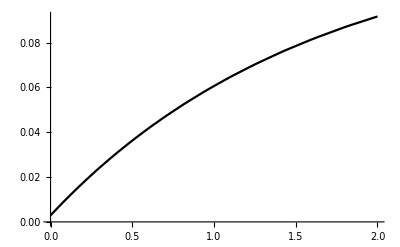

```mathematica
Plot[Gfun[Energy],{Energy,0.,2}]
```

```mathematica
Etest =10^-3;
KFTEITable = Table[{bgrid[[ii]], Sqrt[Afun[Etest]] (KtildeFTEI[bgrid[[ii]],Etest]^-1+Gfun[Etest])^-1 Sqrt[Afun[Etest]]},{ii,1,bn+1}];
```

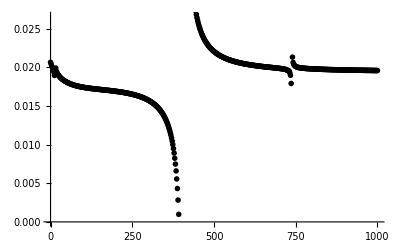

```mathematica
ListPlot[{KFTEITable}]
```

```mathematica
KFTEIfun[B_,Etest_]:= Sqrt[Afun[Etest]](KtildeFTEI[B,Etest]^-1+Gfun[Etest])^-1 Sqrt[Afun[Etest]];
Sfun[B_,Etest_]:= Exp[ⅈ Etafun[Etest]] ((1+ⅈ KFTEIfun[B,Etest])/(1-ⅈ KFTEIfun[B,Etest])) Exp[ⅈ Etafun[Etest]];
ascatfun[B_,Etest_]:=Re[ -1/(ⅈ Sqrt[Etest]) ((Sfun[B,Etest]-1)/(Sfun[B,Etest]+1))];
```

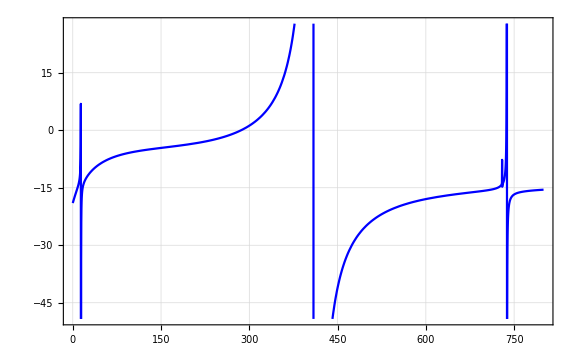

```mathematica
pmqdt3=Plot[{ascatfun[B,(*Etest*)10^-3]*1/BohrinK39vdw},{B,0,800},Frame->True,GridLines->Automatic,ImageSize->Large,PlotStyle->{Blue}]
```

```mathematica
cotdeltafun[Ε_,B_]:=(1-Tan[Etafun[Ε]]KFTEIfun[B,Ε])/(Tan[Etafun[Ε]]+KFTEIfun[B,Ε]);
```

```mathematica
Emin =10^-16*HartreeinK39vdw
Emax = 10^-10*HartreeinK39vdw
```

1.19007×10^-7

0.119007

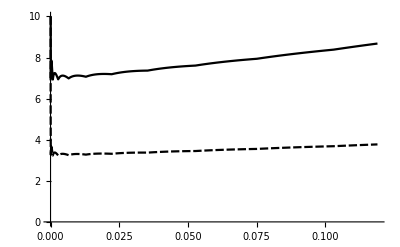

```mathematica
Plot[{√Ε cotdeltafun[Ε,100],√Ε cotdeltafun[Ε,500]},{Ε,Emin,Emax},PlotRange->{0,10}]
```

```mathematica
CalcERE[ΕMin_,ΕMax_,Btest_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{ Εtest,√Εtest cotdeltafun[Εtest,Btest]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
mqdtresdat =Table[{B, CalcERE[10^-2,10^-1,B][[1]]},{B,700,800,.1}];
```

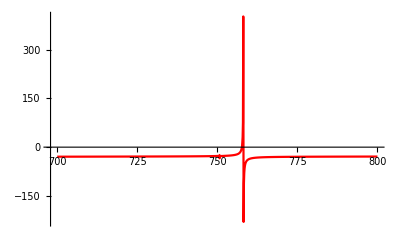

```mathematica
mqdtplot =ListPlot[Table[{mqdtresdat[[i,1]],mqdtresdat[[i,2]]*1/BohrinK39vdw},{i,1,Length[mqdtresdat]}],Joined->True,PlotStyle->Red,PlotMarkers->None,PlotRange->All]
```

```mathematica
logderdat =  Import["/Users/niravmehta/Documents/GitHub/LiScattering/K39FR.dat"];
```

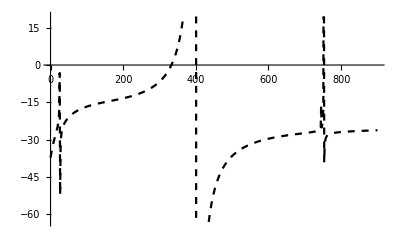

```mathematica
logderplot = ListPlot[logderdat,PlotMarkers->None, Joined->True,PlotStyle->{Dashed}]
```

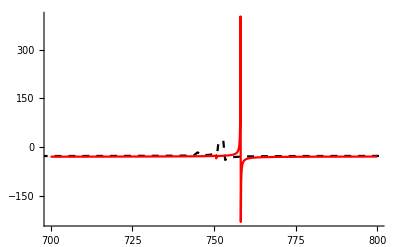

```mathematica
Show[logderplot,mqdtplot,PlotRange->{{700,800},Automatic}]
```

```mathematica
KsrFTEI[B_]:= Transpose[DD[B]].K39SingletProjection.DD[B]*Tan[π K39SingletQD 1.03] + Transpose[DD[B]].K39TripletProjection.DD[B]*Tan[π K39TripletQD 0.96]
```

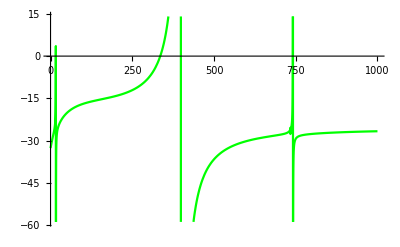

```mathematica
pftnew=Plot[{βK39 abar[0](1-KtildeFTEI[B,10^-14])},{B,0,1000},PlotStyle->{Black,Red,Green}]
```

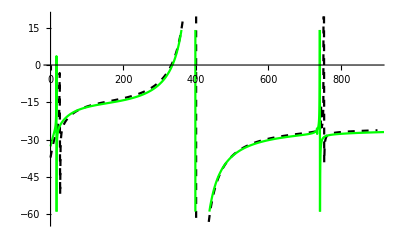

```mathematica
Show[logderplot,pftnew]
```

,Plot

```mathematica
mu39
```

35513.3

```mathematica
mu40
```

36425.

```mathematica
sg40dat =  Import["/Users/alysonlaskowski/Rubidium-Scattering/fort.10"];
tp40dat =  Import["/Users/alysonlaskowski/Rubidium-Scattering/fort.30"];
```

```mathematica
sg40 = Interpolation[sg40dat];
tp40 = Interpolation[tp40dat];
```